# Taylor series

## Definition

```mathematica
SetOptions[{Plot},ImageSize->Scaled[.9],PlotLegends->"Expressions",BaseStyle->{FontFamily->"Helvetica",FontSize->12,Black,Bold}];
SetOptions[{Column,Row},BaseStyle->{FontFamily->"Helvetica",FontSize->12,Black,Bold}];

Manipulate[Column[{
Style[Row[{"y=", Sum[x^y,{y,0,expo}]}],FontColor->Darker@Red],
Plot[{1/(1-x),Sum[x^y,{y,0,expo}]},{x,-2,2},PlotRange->{{-2,2},{-5,20}}]
}],
{ {expo,0,"∑_(x = 0)^n y^x"},0,50,1 }]
```

{x-x^3/6+x^5/120+x^7/5040+x^9/362880,1-x^2/2+x^4/24+x^6/720,Sin[x],Cos[x]}

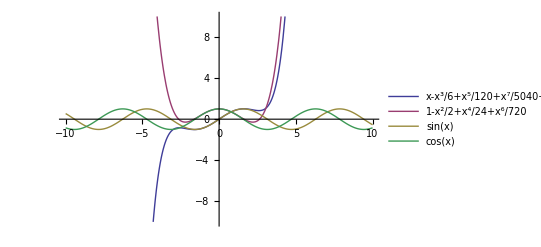

```mathematica
functions = {x-x^3/3!+x^5/5!+x^7/7!+x^9/9!,1-x^2/2!+x^4/4!+x^6/6!,Sin[x],Cos[x]}
Plot[functions,{x,-10,10},PlotRange->{{-10,10},{-10,10}}]
```

```mathematica
CurrentValue["StyleSheetPath"]
```

{FrontEnd`FileName[{$UserBaseDirectory,Autoload,_,FrontEnd,StyleSheets}],FrontEnd`FileName[{$UserBaseDirectory,Applications,_,FrontEnd,StyleSheets}],FrontEnd`FileName[{$BaseDirectory,Autoload,_,FrontEnd,StyleSheets}],FrontEnd`FileName[{$BaseDirectory,Applications,_,FrontEnd,StyleSheets}],FrontEnd`FileName[{$InstallationDirectory,AddOns,Autoload,_,FrontEnd,StyleSheets}],FrontEnd`FileName[{$InstallationDirectory,AddOns,Applications,_,FrontEnd,StyleSheets}],FrontEnd`FileName[{$UserBaseDirectory,SystemFiles,FrontEnd,StyleSheets}],FrontEnd`FileName[{$BaseDirectory,SystemFiles,FrontEnd,StyleSheets}],FrontEnd`FileName[{$InstallationDirectory,Configuration,FrontEnd,StyleSheets}],FrontEnd`FileName[{$InstallationDirectory,SystemFiles,FrontEnd,StyleSheets}]}

```mathematica
$StyleSheetPath
```

$StyleSheetPath